```mathematica
lpr[η_,θ_]=Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ]}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2}});
```

```mathematica
e[η_,θ_]=lpr[η,θ].({{1}, {0}});
```

```mathematica
pEllipse[η_,θ_]=FullSimplify[ComplexExpand[Re[e[η,θ]Exp[-ⅈ t]]],Assumptions->{t>0,0<=η<2π,0<=θ<2π}];
```

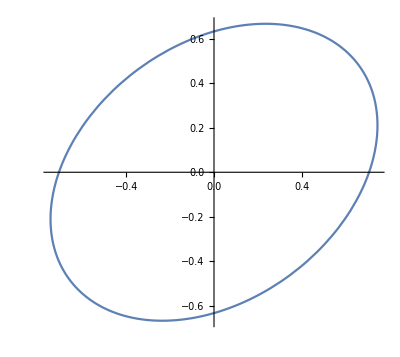

```mathematica
ParametricPlot[pEllipse[π/2,π/180 35.26],{t,0,2π}]
```

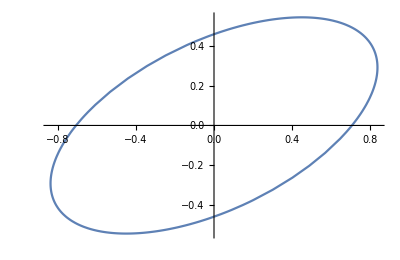

```mathematica
ParametricPlot[pEllipse[π/2,π/180 25.26],{t,0,2π}]
```

```mathematica
Solve[D[(pEllipse[π/2,π/180 10]ᵀ.pEllipse[π/2,π/180 10])[[1,1]],t]==0&&D[(pEllipse[π/2,π/180 10]ᵀ.pEllipse[π/2,π/180 10])[[1,1]],t,t]<0&&0<=t<2π,t]//N
Solve[D[(pEllipse[π/2,π/180 10]ᵀ.pEllipse[π/2,π/180 10])[[1,1]],t]==0&&D[(pEllipse[π/2,π/180 10]ᵀ.pEllipse[π/2,π/180 10])[[1,1]],t,t]>0&&0<=t<2π,t]//N
```

{{t→5.49779},{t→2.35619}}

{{t→3.92699},{t→0.785398}}

```mathematica
pEllipse[π/2,π/180 10]/.t->2.356194490192345
```

{{-0.969846},{-0.17101}}

```mathematica
180/π ArcTan[-0.17101007166283436/-0.9698463103929541]
```

10.

```mathematica
pEllipse[π/2,π/180 10]/.t->2.356194490192345
```